```mathematica
(* NMP5 *)
file5c=<<"/Users/ruppell/Math/temp/NMP5_cpc_clean.txt";
label5c="NMP5 CPC";
file5v=<<"/Users/ruppell/Math/temp/NMP5_cpv_clean.txt"; 
label5v="NMP5 CPV";

yesCPsnuLSP[name_String]:=Select[ToExpression[name<>"v"],#[[3,5,1]]<Abs@#[[3,1,1]]&];
yesCPχ0LSP[name_String]:=Select[ToExpression[name<>"v"],#[[3,5,1]]>Abs@#[[3,1,1]]&];
noCPsnuLSP[name_String]:=Select[ToExpression[name<>"c"],#[[3,5,1]]<Abs@#[[3,1,1]]&];
noCPχ0LSP[name_String]:=Select[ToExpression[name<>"c"],#[[3,5,1]]>Abs@#[[3,1,1]]&];
```

```mathematica
mSnu[name_]:=name[[;;,3,5,1]];
mChi[name_]:=Abs@name[[;;,3,1,1]];
mLSP[name_]:=(Min/@Transpose@{mSnu@name,mChi@name});
```

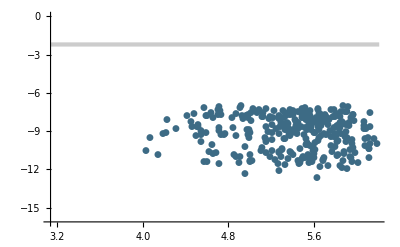

```mathematica
file1=yesCPχ0LSP["file5"];
file2=yesCPsnuLSP["file5"];
file3=noCPχ0LSP["file5"];
file4=noCPsnuLSP["file5"];
p1=ListLogLogPlot[
{Transpose@{file1[[;;,3,5,1]],file1[[;;,5,1]]},
Transpose@{file3[[;;,3,5,1]],file3[[;;,5,1]]},
Transpose@{file2[[;;,3,5,1]],file2[[;;,5,1]]},
Transpose@{file4[[;;,3,5,1]],file4[[;;,5,1]]}},
ImageSize->400,
PlotRange->{Automatic,{10^-7,1}},
PlotStyle->ColorData[31,"ColorList"][[{9,5,8,6}]],
PlotMarkers->Automatic,
AxesOrigin->{23,10^-7},
TicksStyle->Medium,
Prolog->{Opacity[0.2,Black],Rectangle[{Log@23,Log@0.1311},{Log@500,Log@0.0941}]}]
```

```mathematica
Export["/Users/ruppell/Documents/Latex/papers/ScalarDM/NMPplot.eps",p1,"EPS"]
```

/Users/ruppell/Documents/Latex/papers/ScalarDM/NMPplot.eps